```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica-nbs"];
Get["ctmc`"]
```

```mathematica
edges={{1,2},{2,1},{2,3},{3,2},{3,4},{4,3},{4,5},{5,4},{5,6},{6,5},{6,7},{7,6}};
weights={c*kb1,ku1,c*kb2,ku2,c*kb3,ku3,c*kb4,ku4,c*kb5,ku5,c*kb6,ku6};
nstates=7;
nedges=Length[edges];
assum=c>0&&kb1>0&&ku1>0&&kb2>0&&ku2>0&&kb3>0&&ku3>0&&kb4>0&&ku4>0&&kb5>0&&ku5>0&&kb6>0&&ku6>0;
```

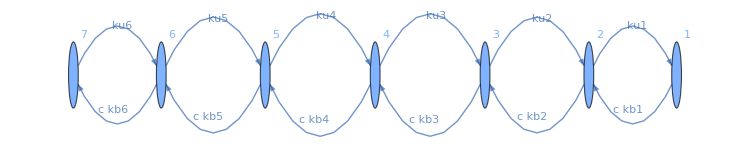

```mathematica
(*Plot the circuit*)
edgeList=Table[edges[[i,1]]->edges[[i,2]],{i,1,nedges}];
g=Graph[edges,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights)[[i]],0.55],{i,1,nedges}],ImageSize->750]
```

```mathematica
Q = RateMatrix[edges, weights, nstates];
ss = SteadyStateProbabilities[Q];

(*Laplace transform of FPTs for individual hitting states*)
k=3;
FoffMat = LaplaceTransformFPT[Q,s1];
```

```mathematica
FonMat = FoffMat/.{s1->s2};
Foff = FoffMat[[k,k+1]][[1]];
```

```mathematica
Fon=FonMat[[k+1,k]][[1]];
```

```mathematica
Poff=InverseLaplaceTransform[Foff,s1,t1];
```

```mathematica
Pon=InverseLaplaceTransform[Fon,s2,t2];
```

```mathematica
integrandOff=Poff*D[Log[Poff],{c,2}]//.{Root[c^3 kb1 kb2 kb3+(c^2 kb1 kb2+c^2 kb1 kb3+c^2 kb2 kb3+c kb3 ku1+c kb1 ku2+ku1 ku2) #1+(c kb1+c kb2+c kb3+ku1+ku2) #1^2+#1^3&,1]->A1,
Root[c^3 kb1 kb2 kb3+(c^2 kb1 kb2+c^2 kb1 kb3+c^2 kb2 kb3+c kb3 ku1+c kb1 ku2+ku1 ku2) #1+(c kb1+c kb2+c kb3+ku1+ku2) #1^2+#1^3&,2]->A2,
Root[c^3 kb1 kb2 kb3+(c^2 kb1 kb2+c^2 kb1 kb3+c^2 kb2 kb3+c kb3 ku1+c kb1 ku2+ku1 ku2) #1+(c kb1+c kb2+c kb3+ku1+ku2) #1^2+#1^3&,3]->A3,
c^2 kb1 kb2+c^2 kb1 kb3+c^2 kb2 kb3+c kb3 ku1+c kb1 ku2+ku1 ku2->D1,(c kb1+c kb2+c kb3+ku1+ku2)->D2,
(2 c kb1 kb2+2 c kb1 kb3+2 c kb2 kb3+kb3 ku1+kb1 ku2)->D3}
```

```mathematica
integrandOn=Pon*D[Log[Pon],{c,2}]//.{};
```

```mathematica
mprocOff = ContinuousMarkovProcess[k,Q];
mprocOn = ContinuousMarkovProcess[k+1,Q];
distOff=FirstPassageTimeDistribution[mprocOff,k+1];
distOn=FirstPassageTimeDistribution[mprocOn,k];

meanToff=Mean[distOff];
meanTon=Mean[distOn];
τ=meanToff+meanTon;
τfun[ci_?NumericQ,kb1_?NumericQ,ku1_?NumericQ,kb2_?NumericQ,ku2_?NumericQ,kb3_?NumericQ,ku3_?NumericQ,kb4_?NumericQ,ku4_?NumericQ,kb5_?NumericQ,ku5_?NumericQ,kb6_?NumericQ,ku6_?NumericQ ]:=Evaluate[τ];
```

```mathematica
integrandOffC=Compile[{{t1,_Real},{c,_Real},{kb1,_Real},{ku1,_Real},{kb2,_Real},{ku2,_Real},{kb3,_Real},{ku3,_Real},{kb4,_Real},{ku4,_Real},{kb5,_Real},{ku5,_Real},{kb6,_Real},{ku6,_Real},{A1,_Real},{A2,_Real},{A3,_Real},{D1,_Real},{D2,_Real},{D3,_Real}},
Evaluate[integrandOff],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
integrandOnC=Compile[{{t1,_Real},{c,_Real},{kb1,_Real},{ku1,_Real},{kb2,_Real},{ku2,_Real},{kb3,_Real},{ku3,_Real},{kb4,_Real},{ku4,_Real},{kb5,_Real},{ku5,_Real},{kb6,_Real},{ku6,_Real},{A1,_Real},{A2,_Real},{A3,_Real},{D1,_Real},{D2,_Real},{D3,_Real}},
Evaluate[integrandOn],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

```mathematica
integrandOffCNum[t1_?NumericQ,c_?NumericQ,kb1_?NumericQ,ku1_?NumericQ,kb2_?NumericQ,ku2_?NumericQ,kb3_?NumericQ,ku3_?NumericQ,kb4_?NumericQ,ku4_?NumericQ,kb5_?NumericQ,ku5_?NumericQ,kb6_?NumericQ,ku6_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=integrandOffC[N[t1],N[c],N[kb1],N[ku1],N[kb2],N[ku2],N[kb3],N[ku3],N[kb4],N[ku4],N[kb5],N[ku5],N[kb6],N[ku6],N[A1],N[A2],N[A3],N[D1],N[D2],N[D3]];

integrandOnCNum[t1_?NumericQ,c_?NumericQ,kb1_?NumericQ,ku1_?NumericQ,kb2_?NumericQ,ku2_?NumericQ,kb3_?NumericQ,ku3_?NumericQ,kb4_?NumericQ,ku4_?NumericQ,kb5_?NumericQ,ku5_?NumericQ,kb6_?NumericQ,ku6_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=integrandOnC[N[t1],N[c],N[kb1],N[ku1],N[kb2],N[ku2],N[kb3],N[ku3],N[kb4],N[ku4],N[kb5],N[ku5],N[kb6],N[ku6],N[A1],N[A2],N[A3],N[D1],N[D2],N[D3]];
```

```mathematica
integrandOffCNum[1,3,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9]
```

-5851.33

```mathematica
ClearAll[FisherFast];
ClearAll[FisherSafe];

FisherFast[c_?NumericQ,kb1_?NumericQ,ku1_?NumericQ,kb2_?NumericQ,ku2_?NumericQ,kb3_?NumericQ,ku3_?NumericQ,kb4_?NumericQ,ku4_?NumericQ,kb5_?NumericQ,ku5_?NumericQ,kb6_?NumericQ,ku6_?NumericQ ]:=Module[{τeval,integral,A1,A2,A3,D1,D2,D3},
τeval=τfun[c,kb1,ku1,kb2,ku2,kb3,ku3,kb4,ku4,kb5,ku5,kb6,ku6];
A1=Root[c^3 kb1 kb2 kb3+(c^2 kb1 kb2+c^2 kb1 kb3+c^2 kb2 kb3+c kb3 ku1+c kb1 ku2+ku1 ku2) #1+(c kb1+c kb2+c kb3+ku1+ku2) #1^2+#1^3&,1];
A2=Root[c^3 kb1 kb2 kb3+(c^2 kb1 kb2+c^2 kb1 kb3+c^2 kb2 kb3+c kb3 ku1+c kb1 ku2+ku1 ku2) #1+(c kb1+c kb2+c kb3+ku1+ku2) #1^2+#1^3&,2];
A3=Root[c^3 kb1 kb2 kb3+(c^2 kb1 kb2+c^2 kb1 kb3+c^2 kb2 kb3+c kb3 ku1+c kb1 ku2+ku1 ku2) #1+(c kb1+c kb2+c kb3+ku1+ku2) #1^2+#1^3&,3];
D1=c^2 kb1 kb2+c^2 kb1 kb3+c^2 kb2 kb3+c kb3 ku1+c kb1 ku2+ku1 ku2;D2=(c kb1+c kb2+c kb3+ku1+ku2);
D3=(2 c kb1 kb2+2 c kb1 kb3+2 c kb2 kb3+kb3 ku1+kb1 ku2);
integral=-NIntegrate[integrandOffCNum[t1,c,kb1,ku1,kb2,ku2,kb3,ku3,kb4,ku4,kb5,ku5,kb6,ku6,A1,A2,A3,D1,D2,D3],{t1,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->6];
integral*c^2/τeval];

FisherSafe[pars__?NumericQ]:=
Quiet[
Check[
FisherFast[pars],
-1,(* ← penalty when NIntegrate fails*)
{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
],{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
];
```

```mathematica
c=1;
kb1=1;
ku1=1;
kb2=1;
ku2=1;
kb3=1;
ku3=1;
kb4=1;
ku4=1;
kb5=1;
ku5=1;
kb6=1;
ku6=1;
FisherSafe[c,kb1,ku1,kb2,ku2,kb3,ku3,kb4,ku4,kb5,ku5,kb6,ku6]
```

0.276465

```mathematica
kmin =0.0001;
kmax = 5;
kdl=0.0888;
cvals=10^Range[-1.,2.,3/13];
cr=5.6;

CloseKernels[];
LaunchKernels[14];                       (*ensure you actually have sub-kernels running*)
DistributeDefinitions[integrandOffC,integrandOffCNum,FisherSafe,cvals,kmin,kmax,kdl];
```

```mathematica
NMaximize[
{FisherSafe[cr,vkb1,vku1,vkb2,vku2,vkb3,vku3,vkb4,vku4,vkb5,vku5,vkb6,vku6],
kmin<=vkb1<=kdl,
kmin<=vkb2<=kdl,
kmin<=vkb3<=kdl,
kmin<=vkb4<=kdl,
kmin<=vkb5<=kdl,
kmin<=vkb6<=kdl,
kmin<=vku1<=kmax,
kmin<=vku2<=kmax,
kmin<=vku3<=kmax,
kmin<=vku4<=kmax,
kmin<=vku5<=kmax,
kmin<=vku6<=kmax},
{vkb1,vku1,vkb2,vku2,vkb3,vku3,vkb4,vku4,vkb5,vku5,vkb6,vku6},
Method->"NelderMead",
PrecisionGoal->6,AccuracyGoal->20,MaxIterations->10,
EvaluationMonitor:>Sow[FisherSafe[cr,vkb1,vku1,vkb2,vku2,vkb3,vku3,vkb4,vku4,vkb5,vku5,vkb6,vku6]]
]
```

$Aborted

```mathematica
reults1={1.2856368676659315,{vkb1->0.0001,vku1->4.934920104367113,vkb2->0.05525665947860478,vku2->3.410194443992551,vkb3->0.0001,vku3->4.995099102772477,vkb4->0.065116121014587,vku4->0.06903968000637122,vkb5->0.0014948005369557816,vku5->0.053991670159255094,vkb6->0.06781743362980698,vku6->4.520330534425437}}
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {5,1,3};
onStates = {6,2,4};
F5on = LaplaceTransformToSetByState[Q2,5,onStates,s1];
```